```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

{{x→-0.916058},{x→-0.147995+0.69178 ⅈ},{x→-0.147995-0.69178 ⅈ},{x→0.52675},{x→-0.0647024}}

{{x→-0.25},{x→-0.25},{x→0.},{x→0.}}

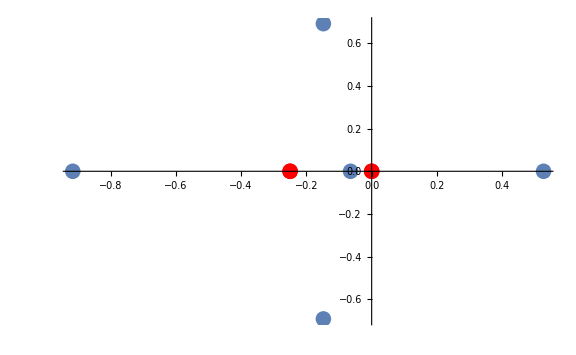

```mathematica
(*potential=Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x]/.{δ->1,β->1};*)
potential=Function[z,1/4 (1/z^2-4 z+(4 β^2)/z-4 δ^2-3/((z+δ^2)^2)+(2-4 β δ)/(z^2+z δ^2))/.{δ->0.5,β->0.1}];
zeros=NSolve[potential[x]==0,x]
poles=NSolve[potential[x]^-1==0,x]
(*ListPlot[Table[{Re[x/.poles[[i]]],Im[x/.poles[[i]]]},{i,1,Length[poles]}],PlotStyle->Red]*)
Show[ListPlot[Table[{Re[x/.zeros⟦i⟧],Im[x/.zeros⟦i⟧]},{i,1,Length[zeros]}]],ListPlot[Table[{Re[x/.poles⟦i⟧],Im[x/.poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red],ImageSize->Large]
```

-781.29+1/(4 z^2)+12.5/z

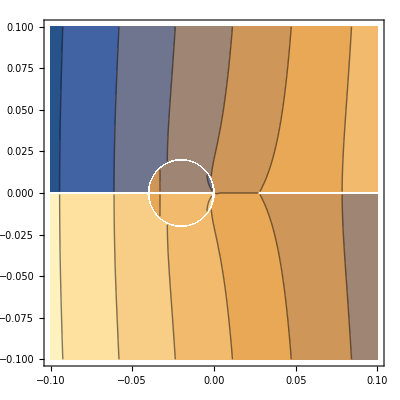

```mathematica
values={β->0,δ->0.2};
Series[1/4 (1/z^2-4 z+(4 β^2)/z-4 δ^2-3/((z+δ^2)^2)+(2-4 β δ)/(z^2+z δ^2)),{z,0,0}]/.values//Normal
Integrate[ⅈ √%,z];
ComplexExpand[Re[%/.z->x+ⅈ y]];
ContourPlot[%,{x,-0.1,0.1},{y,-0.1,0.1}]
```

-30.8642-3/(4 (0.09+z)^2)-5.55556/(0.09+z)

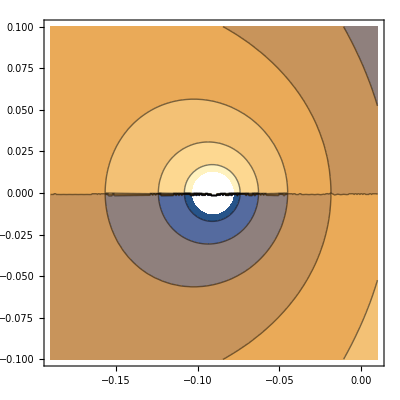

```mathematica
values={β->0,δ->0.3};
Series[1/4 (1/z^2-4 z+(4 β^2)/z-4 δ^2-3/((z+δ^2)^2)+(2-4 β δ)/(z^2+z δ^2)),{z,-δ^2,0}]/.values//Normal
Integrate[ⅈ √%,z];
ComplexExpand[Re[%/.z->x+ⅈ y]];
ContourPlot[%,{x,(-δ^2/.values)-l,(-δ^2/.values)+l},{y,-l,l}]
```

{{z→-0.611438},{z→-0.0619715+0.545788 ⅈ},{z→-0.0619715-0.545788 ⅈ},{z→0.487879},{z→-0.0224983}}

-154.411+0.25/z^2+5.55556/z

-30.8642-0.75/(0.09+z)^2-5.55556/(0.09+z)

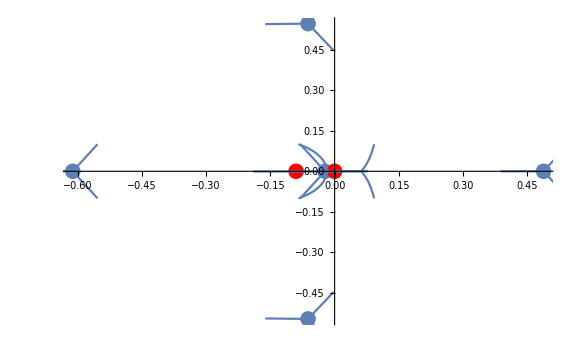

```mathematica
values={β->0,δ->0.3};l=0.1;
potential=Q[δ^2/(x(x+δ^2)),-(x+δ^2-β^2/x+(β δ)/(x(x+δ^2))),x]/.values;
zeroFolations={};
zeros=NSolve[potential[z]==0,z]/.values
For[i=1,i≤Length[zeros],i++,
ser=Series[potential[z],{z,(z/.zeros⟦i⟧),1}];
norm=ser/Abs[SeriesCoefficient[ser,1]]//Normal;
int=Integrate[ⅈ √norm,z];
real=ComplexExpand[Re[int/.z->x+ⅈ y]];
zeroFolations=AppendTo[zeroFolations,ContourPlot[real==0,{x,Re[z/.zeros⟦i⟧]-l,Re[z/.zeros⟦i⟧]+l},{y,Im[z/.zeros⟦i⟧]-0.1,Im[z/.zeros⟦i⟧]+0.1}]];
];

poleFolations={};poles={{z->0},{z->(-δ^2/.values)}};
Series[potential[z],{z,0,0}]/.values//Normal
Integrate[ⅈ √%,z];
ComplexExpand[Re[%/.z->x+ⅈ y]];
AppendTo[poleFolations,ContourPlot[%==0,{x,-l,l},{y,-l,l}]];

Series[potential[z],{z,(-δ^2/.values),0}]//Normal
Integrate[ⅈ √%,z];
ComplexExpand[Re[%/.z->x+ⅈ y]];
AppendTo[poleFolations,ContourPlot[%==0,{x,(-δ^2/.values)-l,(-δ^2/.values)+l},{y,-l,l}]];

Show[ListPlot[Table[{Re[z/.zeros⟦i⟧],Im[z/.zeros⟦i⟧]},{i,1,Length[zeros]}]],ListPlot[Table[{Re[z/.poles⟦i⟧],Im[z/.poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->Red],zeroFolations,poleFolations,ImageSize->Large]
Clear[ser,norm,int,real,i]
```

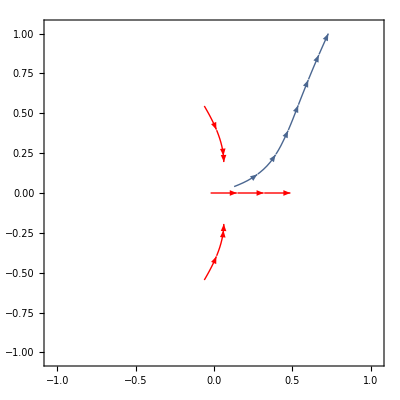

```mathematica
potential[z];
StreamPlot[{Cos[1/2 Arg[%/.z->x+ⅈ y]],-Sin[1/2 Arg[%/.z->x+ⅈ y]]},{x,-1,1},{y,-1,1},StreamPoints->{Table[{{Re[z/.zeros⟦i⟧],Im[z/.zeros⟦i⟧]},Red},{i,1,Length[zeros]}],Automatic}]
```

```mathematica
Table[{Re[z/.zeros⟦i⟧],Im[z/.zeros⟦i⟧]},{i,1,Length[zeros]}]
```

{{-0.611438,0},{-0.0619715,0.545788},{-0.0619715,-0.545788},{0.487879,0},{-0.0224983,0}}